```mathematica
SetDirectory[NotebookDirectory[]];
Get["Kimberling.m"]; 
Get["ConicTools.m"];
```

```mathematica
PA={10+1/3,7.8881063774661547234231043887488227312206683077257870971729595588570966121408707156876700362441455708}; PB={0,0}; PC={6,0};
```

```mathematica
(* Calculate ellipses *)
X1 =KimberlingCenter[1,PA,PB,PC];
elc = ellipseFociEq[PA[[1]],PA[[2]],PB[[1]],PB[[2]],X1[[1]],X1[[2]]]//Simplify;
elb = ellipseFociEq[PC[[1]],PC[[2]],PA[[1]],PA[[2]],X1[[1]],X1[[2]]]//Simplify;
ela = ellipseFociEq[PB[[1]],PB[[2]],PC[[1]],PC[[2]],X1[[1]],X1[[2]]]//Simplify;
{EA, EB,EC}=ImplicitRegion[matrixToEq[#]==0,{x,y}]&/@{ela,elb,elc};

(* Select the other intersection point of the ellipses, not X1 *)
chorda=NSolve[matrixToEq[elb]==0 &&matrixToEq[elc]==0,{x,y}, Reals];
{xa, ya} = If[Abs[X1[[1]] - (x/.chorda[[1]])]<10^-10&&Abs[X1[[2]] - (y/.chorda[[1]])]<10^-10,{x/.chorda[[2]], y/.chorda[[2]]}, {x/.chorda[[1]], y/.chorda[[1]]}];

chordb=NSolve[matrixToEq[ela]==0 &&matrixToEq[elc]==0,{x,y}, Reals];
{xb, yb} = If[Abs[X1[[1]] - (x/.chordb[[1]])]<10^-10&&Abs[X1[[2]] - (y/.chordb[[1]])]<10^-10,{x/.chordb[[2]], y/.chordb[[2]]}, {x/.chordb[[1]], y/.chordb[[1]]}];

chordc=NSolve[matrixToEq[ela]==0 &&matrixToEq[elb]==0,{x,y}, Reals];
{xc, yc} = If[Abs[X1[[1]] - (x/.chordc[[1]])]<10^-10&&Abs[X1[[2]] - (y/.chordc[[1]])]<10^-10,{x/.chordc[[2]], y/.chordc[[2]]}, {x/.chordc[[1]], y/.chordc[[1]]}];

linea = Simplify[lineEq[xa, ya, PA[[1]], PA[[2]]]];
lineb = Simplify[lineEq[xb, yb, PB[[1]], PB[[2]]]];
linec = Simplify[lineEq[xc, yc, PC[[1]], PC[[2]]]];
```

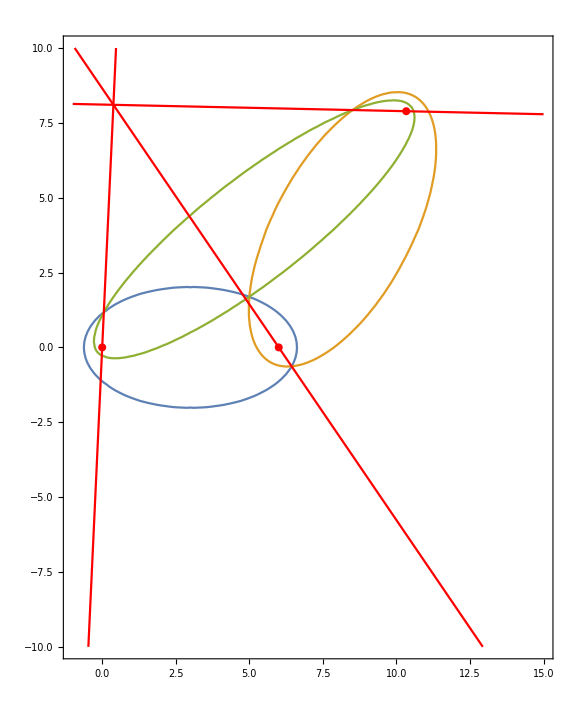

```mathematica
Show[
ContourPlot[{matrixToEq[ela]==0, matrixToEq[elb]==0,matrixToEq[elc]==0} ,
{x,-1,15},{y,-10,10},
AspectRatio->Automatic, ImageSize->Large, 
Epilog->{PointSize[0.01],Red,Point[#]&/@{PA, PB, PC}}
]
, ContourPlot[{linea==0, lineb==0, linec==0} ,{x,-1,15},{y,-10,10}, ContourStyle->Red]
]
```

```mathematica
solc=First[SolveValues[linea==0&&lineb==0,{x,y}]];
solb=First[SolveValues[linea==0&&linec==0,{x,y}]]
solc-solb
```

{0.3810278815303058166206870775310326275256284658028171851432872370121760858545679979923119817698,8.10163695811335726329762040637643990833606782884937519368716942916329450610854232759875787367}